## RBSim` Documentation

### Preamble

```mathematica
Needs["RBSim`"]
Needs["Visualization`"]
```

The following packages are needed to run some code found in this documentation notebook.

### Source Code

Open Source Code

## Introduction and Overview

This package provides generic tools for simulating Randomized Benchmarking (RB) and related protocols. Though RB is in the title of this package, it should be general enough to simulate any kind of protocol which relies on a gate set whose gates are specified by pulses.
The main advantage of this library is that it allows a wide class of error models. In particular, all of the following error models can be incorporated simultaneously:
    • Discrete error channels following any pulse, which may be gate dependent, independent, or depend on exactly which pulses preceded the present pulse.
    • Hardware distortions (for example, from a transfer function) applied to the entire concatenated pulse train of a given pulse sequence.
    • Coupling to an external quantum system.
    • Additive stochastic Hamiltonian noise, including on the bath.
    • Static parameter noise; noise chosen randomly at the beginning of each pulse sequence, but fixed for the duration of the sequence.

#### References

## Gate Sets

GateSet is a Head used to store all relevant information about a particular set of quantum gates,  their structure, and their Hamiltonian implementation.  Such objects have the format gateSet=GateSet[key1→value1,...]. 

Retrieving Values
Values of keys can be retrieved by calling the key: Dimension[gateSet]

Notes
• A gate set is formatted as GateSet[“name”] when printed -- do not let this fool you about the contents. Use FullForm[gateSet] or List@@gateSet to see all of the explicit contents.

Possible Keys
GateSetName
Size
Dimension
GateProduct
GateInverse
GateUnitary
GatePulse

GateNoiseGateSet is a Head used to store all relevant information about a particular set of quantum gates and their structure, along with a GateNoise error model.  Such objects have the format gateSet=GateNoiseGateSet[key1→value1,...]. 

This object is a combination of GateSet and NoiseModel where the only noise is GateNoise, that is, all noise happens as a discrete CPTP map. There is no implementation of the gate as a pulse; it is assumed that all noise is in the GateNoise. 

Retrieving Values
Values of keys can be retrieved by calling the key: Dimension[gateSet]

Notes
• A gate set is formatted as GateNoiseGateSet[“name”] when printed -- do not let this fool you about the contents. Use FullForm[gateSet] or List@@gateSet to see all of the explicit contents.
•  This object can be created manually, or compiled from a GateSet and NoiseModel with CompileGateSet.

Possible Keys
GateSetName
Size
Dimension
GateProduct
GateInverse
GateUnitary
GateNoise

### GateSet Keys

GateSetName is a GateSet key storing a string with a human-readable gate set name.

Size is a GateSet key storing the number of gates in the gate set.

Dimension is a GateSet key storing the Hilbert space dimension the gates in the gate set act on.

GateProduct is an optional GateSet key storing a function f[i,j] that takes two gate indices and returns the index of the product gate. Gate i happens before gate j, so the product is gate[j].gate[i].

GateInverse is an optional GateSet key storing a function f[i] that takes a gate index and returns the index of the inverse gate.

GateUnitary is a GateSet key storing a function f[i] that returns the matrix representation of the gate with index i.

GatePulse is a GateSet key storing a function f[i] that returns the pulse (in a format accepted by QSim`PulseSim) of the gate with index i.

GateNoise (for GateNoiseGateSet only)

### Built-In GateSets

$gaussianQubitGateSet is a 12-element unitary 2-design for qubits implemented with gaussian pulses applied on the x-y plane for all gates.

#### Example: Qubit 2-design group with Gaussian pulses

```mathematica
Size[$gaussianQubitGateSet]
Dimension[$gaussianQubitGateSet]
```

12

2

```mathematica
GateUnitary[$gaussianQubitGateSet]/@Range[12]//MatrixListForm
```

(1 | 0
0 | 1),(1/2+ⅈ/2 | -1/2+ⅈ/2
1/2+ⅈ/2 | 1/2-ⅈ/2),(-ⅈ | 0
0 | ⅈ),(1/2-ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | 1/2+ⅈ/2),(1/2-ⅈ/2 | -1/2-ⅈ/2
1/2-ⅈ/2 | 1/2+ⅈ/2),(1/2-ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | 1/2+ⅈ/2),(1/2+ⅈ/2 | -1/2-ⅈ/2
1/2-ⅈ/2 | 1/2-ⅈ/2),(1/2-ⅈ/2 | -1/2+ⅈ/2
1/2+ⅈ/2 | 1/2+ⅈ/2),(1/2+ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | 1/2-ⅈ/2),(1/2+ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | 1/2-ⅈ/2),(0 | -1
1 | 0),(0 | ⅈ
ⅈ | 0)

```mathematica
Row[
PulsePlot[ToPulse@First@GatePulse[$gaussianQubitGateSet][#],ImageSize->100,PlotTheme->"Detailed",PlotLabel->DistributeOption["X"<>ToString[#],"Y"<>ToString[#]]]&/@Range[12]
]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
GateProduct[$gaussianQubitGateSet][2,3]
```

6

### GateSet Diagnostics

FramePotential[gs_GateSet, t] returns the t-frame potential of the given GateSet.

TestGateSetPulses[gs_GateSet]  simulates the pulses (with no drift Hamiltonian) and compares the result with the ideal unitary.

Options
• GateIndeces is All or a list of gate indices to perform the test on.
• TakeOverlap is boolean specifying whether to return overlaps or difference matrices. Default is True.

TestGateSetInverses[gs_GateSet] uses the gs inverse function GateInverse to multiply gates with their supposed inverses. By default, a list of overlaps with the identity matrix is returned.

Options
• GateIndeces is All or a list of gate indices to perform the test on.
• TakeOverlap is boolean specifying whether to return overlaps or difference matrices. Default is True.

TestGateSetProducts[gs_GateSet] uses the gs product function GateProduct to multiply gate matrices together. By default, a list of overlaps is returned.

Options
• GateIndeces is All or a list of gate indices to perform the test on.
• TakeOverlap is boolean specifying whether to return overlaps or difference matrices. Default is True.

GateIndeces is an option for TestGateSetPulses, TestGateSetInverses, and TestGateSetProducts specifying which indices or pairs of indices to test. Default is All.

TakeOverlap is a boolean option for TestGateSetPulses, TestGateSetInverses, and TestGateSetProducts specifying whether to return full matrices, or just the relevant overlaps.

#### Example: FramePotential

Compute the frame potential of the built in gate set $gaussianQubitGateSet

```mathematica
FramePotential[$gaussianQubitGateSet,2]
```

2

#### Example: Tests

All pulses have unit overlap with the ideal matrices:

```mathematica
TestGateSetPulses[$gaussianQubitGateSet]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

The following demonstrates the gate product function GateProduct[$gaussianQubitGateSet] is working correctly by testing it against actual matrix multiplication:

```mathematica
TestGateSetProducts[$gaussianQubitGateSet]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

The following demonstrates the gate inverse function GateInverse[$gaussianQubitGateSet] is working correctly by testing it against actual matrix inversion:

```mathematica
TestGateSetInverses[$gaussianQubitGateSet]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

## Noise Models

NoiseModel is a Head used to store all relevant information about a particular noise model.  Such objects have the format noiseModel=NoiseModel[key1→value1,...]. 

Retrieving Values
Values of keys can be retrieved by calling the key: GateNoise[gateSet]

Possible Keys
GateNoise
DistortionMultiplier
DistortionOperator
StochasticNoise
StaticNoise
Generator
StepSize

### GateNoise Keys

GateNoise is a NoiseModel key storing a function  f[i1,i2,...,in] that returns an object satisfying ChannelPulseQ given the gate index history i1,i2,...,in where in is the most recent.

DistortionMultiplier is a NoiseModel key storing a number specifying how many output pulse steps there are per input pulse step. This is only relevant when the noise model has a DistortionOperator set. The important use of this property is that in simulation of a pulse sequence, the end of the i’th pulse is calculated as this number times the total number of input time steps until the end of the i’th pulse.

DistortionOperator is a NoiseModel key storing a DistortionOperator, as defined in the GRAPE` package,  to be used on any concatenated pulse sequence.

StochasticNoise is a NoiseModel key storing a list of random function symbols along with their random functions, for example, {γ \[Distributed] WeinerProcess[0,0.1], δ \[Distributed] OrnsteinUhlenbeckProcess[1,2,3]}. The distributed symbol is typed with escape+dist+escape.

StaticNoise is a NoiseModel key storing a list of symbols and their corresponding distributions, for example, {{x,y} \[Distributed] MultinormalDistribution[{0,1},{{1,0},{0.5,1}}], ξ \[Distributed] BetaDistribution[1,2]}. The distributed symbol is typed with escape+dist+escape.

Generator is a NoiseModel key which specifies a Hamiltonian matrix or LindbladForm of the system. This can possibly act on a Hilbert space larger than that of the gate set.

StepSize is a NoiseModel key storing a number representing the step size of time slicing in the quantum dynamics simulator.

### Example: GateNoise

## Protocols

Protocol is a Head used to store all relevant information about a particular protocol.  Such objects have the format protocol=Protocol[key1→value1,...]. 

Retrieving Values
Values of keys can be retrieved by calling the key: ProtocolName[gateSet]

Notes
• A gate set is formatted as Protocol[“name”] when printed -- do not let this fool you about the contents. Use FullForm[protocol] or List@@protocol to see all of the explicit contents.

Possible Keys
ProtocolName
SequenceLengths
ExperimentTypes
NumSequenceDraws
NumRepetitions
SequenceGenerator
SimulationOptions
SimulationParser
ParallelOptions
TotalGates

### Protocol Keys

ProtocolName is a Protocol key storing a human readable string describing the protocol.

SequenceLengths is a Protocol key storing a list of integers specifying the lengths of sequences to use.

ExperimentTypes is a Protocol key storing a function f[M] that returns a list of experiment types for the sequence length M. The list can contain any types of values; they are used by SequenceGenerator.

NumSequenceDraws is a Protocol key storing a function f[M,e] that returns an integer specifying the number of random draws to take using Sequence generator at the sequence length M and experiment type e.

NumRepetitions is a Protocol key storing a function f[M,e,i] that returns an integer specifying the number of random draws to take at sequence length M, experiment type e, and sequence draw i.

SequenceGenerator is a Protocol key storing a function seqGen[gs,{M,e,i}] that takes a GateSet along with a sequence length M, experiment type e, and sequence draw index i and returns a gate sequence, which is a list of indices corresponding to gates from gs.

SimulationOptions is a Protocol key storing a list of options to pass to the simulator, such as InitialState.

SimulationParser is a Protocol key storing a function which acts on the output of PulseSim to return the quantity of interest.

ParallelOptions is a Protocol key storing a list of options to be passed to ParallelTable during simulation.

TotalGates is a Protocol key storing how many gates need to be implemented in total to perform the entire protocol. Used for the simulation progress monitor.

### Built-in Protocols

RBDraw[gateSet, seqLength] is a helper function that returns a list of gate indices of length seqLength+1, such that the total product according to gs is the identity unitary. The gateSet requires the keys GateProduct and GateInverse to be implemented.

RBProtocol[seqLengths,numSeqs,shotsPerSeq,ρ,E] returns a Protocol object specifying the standard RB protocol, with sequences whose lengths are given by the list seqLengths. For every sequence length, numSeqs different random sequences are drawn, and each random sequence is repeated shotPerSeq number of times. ρ is the initial density matrix, and E is the observable.

#### Example

Create an instance of the RB protocol with 10 draws of each of the sequence lengths 2,4,10, and 2 repetitions per draw. We initialize and measure the |0⟩ state.

```mathematica
rb=RBProtocol[{2,4,10},10,2,{{1,0},{0,0}},{{1,0},{1,0}}];
```

Note that there is only one ExperimentType, named 0.

```mathematica
TotalGates[rb]
ExperimentTypes[rb][10]
```

380

{0}

Get a sequence of length 10 (plus an inversion) with experiment type 0, and random draw index 1:

```mathematica
seq=SequenceGenerator[rb][$gaussianQubitGateSet,{10,0,1}]
```

{1,6,11,4,11,5,3,2,12,9,4}

These are the unitaries they correspond to:

```mathematica
GateUnitary[$gaussianQubitGateSet]/@seq//MatrixListForm
```

(1 | 0
0 | 1),(1/2-ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | 1/2+ⅈ/2),(0 | -1
1 | 0),(1/2-ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | 1/2+ⅈ/2),(0 | -1
1 | 0),(1/2-ⅈ/2 | -1/2-ⅈ/2
1/2-ⅈ/2 | 1/2+ⅈ/2),(-ⅈ | 0
0 | ⅈ),(1/2+ⅈ/2 | -1/2+ⅈ/2
1/2+ⅈ/2 | 1/2-ⅈ/2),(0 | ⅈ
ⅈ | 0),(1/2+ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | 1/2-ⅈ/2),(1/2-ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | 1/2+ⅈ/2)

Check that they multiply to the identity. Notice the Reverse, because by convention, this package always lists gates chronologically.

```mathematica
Fold[Dot,Reverse[GateUnitary[$gaussianQubitGateSet]/@seq]]//MatrixForm
```

(-1 | 0
0 | -1)

## Compilers

### CompileSequence and CompiledSequence

CompileSequence[gs_GateSet,sequence,nm_NoiseModel] compiles the gates from the GateSet gs corresponding to the sequence of gate indices sequence under the given NoiseModel nm. The gate indices are integers between 1 and Size[gs], and should appear in chronological order, that is,
the first element of sequence is the first gate applied.

The output of this function a CompiledSequence object.

CompiledSequence is a Head used to store a compiled version of the relevant information needed to simulate a specific gate sequence under some model, as output by the CompileSequence function.  Such objects have the format compiledSequence=CompiledSequence[key1→value1,...]. 

Retrieving Values
Values of keys can be retrieved by calling the key: Generator[gateSet]

Possible Keys
Generator
PulseSequence
StepSize
GateSequence
UndistortedLongPulse
GateSet
NoiseModel

#### CompiledSequence Keys

Generator

PulseSequence is a CompiledSequence key storing a list of operations to be performed by PulseSim. This list should satisfy PulseSequenceQ.

StepSize

GateSequence is a CompiledSequence key storing a list of integers corresponding to gates from a given GateSet. The gate indices are integers between 1 and Size[gateSet], and should appear in chronological order, that is, the first element of sequence is the first gate applied.

UndistortedLongPulse is a CompiledSequence key storing the catenated pulse sequence  before the DistortionOperator (if any) is applied.

GateSet

NoiseModel

#### Example

Compile gates 12,10,2 of the $gaussianQubitGateSet under a distortion noise model.

```mathematica
nm=NoiseModel[DistortionOperator->FastExponentialDistortion[0.01,4,20]];
compiledSequence=CompileSequence[$gaussianQubitGateSet,{12,10,2},nm];
```

```mathematica
GateSequence[compiledSequence]
```

{12,10,2}

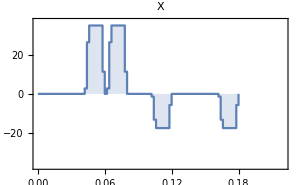
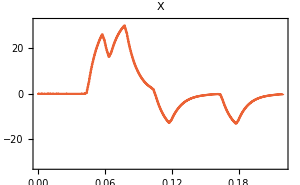
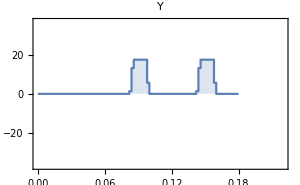
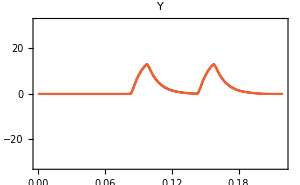

```mathematica
PlotSequence[compiledSequence,ImageSize->300,PlotLabel->DistributeOption["X","Y"]]
```

### CompileGateNoise

CompileGateNoise[gs_GateSet, nm_NoiseModel,depth]

## Simulators

SimulateSequence[seq_CompiledSequence,OptionsPattern[PulseSim]] simulates the given the CompiledSequence seq generated by CompileSequence using PulseSim and its provided options. The output is the output of PulseSim.

SimulateProtocol[gs_GateSet,ns_NoiseModel,protocol_Protocol] simulates the given protocol with the given gate set gs under the noise model ns. The output is an array of results whose shape depends on the protocol; if the properties ExperimentTypes, NumSequenceDraws, NumRepetitions are all constant, the output will be an array with dimensions {numSeqLengths, numExpTypes, numSeqDraws, numReps}. Otherwise, the output will be ragged, but with the same index types.

### Example: SimulateProtocol with GateSet and NoiseModel

Set up a noise model and a protocol and simulate.

```mathematica
(* Run this for parallelization: LaunchKernels[]; ParallelNeeds["RBSim`"]; *)
nm=NoiseModel[
DistortionOperator->FastExponentialDistortion[0.01,4,20],
GateNoise->IndependentNoise[Kraus[{Sqrt[0.01]TP[X],Sqrt[0.99]TP[I]}]],
DistortionMultiplier->4
];
protocol=RBProtocol[
{1,2,100},
30,1,
Projector[{1,0}],Projector[{1,0}]
];
SimulateProtocol[
$gaussianQubitGateSet,
nm,
protocol
]
```

{24.2979,Null}

## Visualization

### PlotSequence

PlotSequence[seq_CompiledSequence,OptionsPattern[PulsePlot]] plots the pulse profile of some CompiledSequence object seq.

#### Example

Compile gates 12,10,2 of the $gaussianQubitGateSet under a distortion noise model and plot it.

```mathematica
nm=NoiseModel[DistortionOperator->FastExponentialDistortion[0.01,4,20]];
compiledSequence=CompileSequence[$gaussianQubitGateSet,{12,10,2},nm];
PlotSequence[compiledSequence,ImageSize->300,PlotLabel->DistributeOption["X","Y"]]
```

-Graphics--Graphics--Graphics--Graphics-